```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
Clear[β]
```

```mathematica
T[t_,m_]:=T[t,m]=ReplacePart[0*IdentityMatrix[m],Join[Table[{x,x+1},{x,Range[1,m,4]}],Table[{x,x-1},{x,Range[4,m,4]}]]->t]
```

```mathematica
Clear[leadgenerateleft]
```

```mathematica
leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[m]-unit.T[t,m].J.ConjugateTranspose[T[t,m]]].unit,50000];J=J]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= If[Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]>25,25,Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]]
```

```mathematica
Monitor[Export["~/Downloads/PhD_new/PhD/fwi/zgnr/10zgnr/CA_0.DAT",Table[{ω,tr1[ω,0.001,1,0,10]},{ω,Range[0,3,0.01]}]],ω]
```

~/Downloads/PhD_new/PhD/fwi/zgnr/10zgnr/CA_0.DAT

```mathematica
F[n_]:= {n,n}
```

```mathematica
unit[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,δ,t,ϵ,50]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{1,50}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,num1_,num2_,n1_,n2_]:=Module[{list,b2},
list={RandomSample[Join[Table[unit[ω,0.001,1,0,ϵ1,n1],num1],Table[unit[ω,0.001,1,0,ϵ1,n2],num2] ,Table[unit[ω,0.001,1,0,0,1],100-num2-num1]]]};
sl1= Module[{J=SL[ω,0.001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[list[[1,ζ]]].T[t,m].J.ConjugateTranspose[T[t,m]]].Inverse[list[[1,ζ]]],{ζ,1,100}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.ConjugateTranspose[T[t,m]].leadgenerateleft[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]]].sl1;
Ir1:=Inverse[IdentityMatrix[m]-leadgenerateleft[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].sl1.ConjugateTranspose[T[t,m]]].leadgenerateleft[ω,0.001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];{Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]],If[Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]]>45,45,Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]]]}]
```

```mathematica
device[1.5,0.001,1,0,0.5,50,10,0,1,0]//AbsoluteTiming
```

{1.5177,18.0345}

```mathematica
Clear[tra]
```

```mathematica
tra:=tra=ParallelTable[{ω,device[ω,0.001,1,0,0.5,50,50,0,1,0][[2]]},{ω,Range[0,3,0.01]}]
```

```mathematica
tra1:=Table[tra[[x]],{x,51,299}]
```

```mathematica
Export["~/PhD/quantum_sudoq/tra1.dat",tra1]
```

~/PhD/quantum_sudoq/tra1.dat

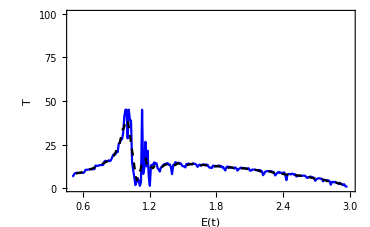

```mathematica
ListLinePlot[{tra1,MovingAverage[tra1,8]},PlotRange->{{0.5,3},{0,100}},Frame->True,PlotStyle->{Blue,Directive[Dashed,Black]},FrameLabel->{{HoldForm[Τ],None},{HoldForm[Ε[t]],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",20,GrayLevel[0.1]},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black],Frame->True,ImageSize->{1100,785}]
```

```mathematica
Mean[ParallelTable[device[0,0.0001,1,0,0.5,10,50,0,1,0],2000]]
```

2.27563

```mathematica
Table[Print["Working on === "<>ToString[num]<>"...."];Export["/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_"<>ToString[num]<>".DAT",Table[{ω,Mean[ParallelTable[device[ω,0.0001,1,0,0.5,20,num,0,1,0],2000]]},{ω,Range[0,3,0.01]}]],{num,Range[5,95,5]}]
```

Working on === 5....

Working on === 10....

Working on === 15....

Working on === 20....

Working on === 25....

Working on === 30....

Working on === 35....

Working on === 40....

Working on === 45....

Working on === 50....

Working on === 55....

Working on === 60....

Working on === 65....

Working on === 70....

Working on === 75....

Working on === 80....

Working on === 85....

Working on === 90....

Working on === 95....

{/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_5.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_10.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_15.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_20.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_25.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_30.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_35.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_40.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_45.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_50.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_55.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_60.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_65.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_70.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_75.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_80.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_85.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_90.DAT,/home/shardulmukim/PhD/fwi/zgnr/20zgnr/CA_95.DAT}

```mathematica
transmission=Table[Import["/home/shardulmukim/PhD/fwi/zgnr/10zgnr/CA_"<>ToString[x]<>".DAT"],{x,Range[5,95,5]}]
```

{{{0.,2.29791},{0.01,0.797487},{0.02,0.815223},{0.03,0.787112},{0.04,0.745662},{0.05,0.694959},290,{2.96,6.7568×10^-7},{2.97,5.02757×10^-7},{2.98,3.91408×10^-7},{2.99,3.13533×10^-7},{3.,2.5746×10^-7}},17,{1}}
 |  |  |  |

```mathematica
%160//Dimensions
```

{19,301,2}

```mathematica
input= Table[ParallelTable[{ω,device[ω,0.0001,1,0,0.5,10,50,0,1,0]},{ω,Range[0,3,0.01]}],1000]
```

{{{0.,2.02996},{0.01,0.133944},{0.02,0.682925},{0.03,0.120735},{0.04,0.0443085},{0.05,0.665051},290,{2.96,6.86665×10^-7},{2.97,5.11773×10^-7},{2.98,3.96904×10^-7},{2.99,3.17351×10^-7},{3.,2.59936×10^-7}},999}
 |  |  |  |

```mathematica
misfit1[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1:=Table[Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[f]][[1;;301,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{f,19}];
list=Transpose[Join[{Range[5,95,5]},{ρ1}]];Abs[list[[Position[list,Min[list]][[1,1]]]][[1]]-50]/50]
```

```mathematica
misfit1[3,0.1,2]
```

0

```mathematica
Table[misfit1[3,0.1,n],{n,100}]
```

{0,0,1/10,0,0,0,0,0,1/10,1/10,1/10,1/5,0,1/10,0,0,1/10,1/10,0,1/10,1/10,1/5,1/10,0,1/10,1/10,0,1/10,1/10,0,0,0,1/10,0,0,1/10,0,1/10,0,0,1/10,0,1/10,0,0,0,0,0,1/10,0,0,0,0,0,0,1/5,0,0,1/10,0,1/10,1/10,0,1/10,0,1/10,0,1/10,1/10,1/10,0,1/10,1/5,2/5,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,0,1/10,0,0,0,0,0,1/10,1/10,0,0,1/10,1/5,1/10,1/10,1/10,0,1/10}

```mathematica
Table[{x,Print["Working on =="<>ToString[x]<>"..."];Mean[Table[misfit1[x,0.1,n],{n,100}]]},{x,Range[0.3,3,0.3]}]
```

Working on ==0.3...

Working on ==0.6...

Working on ==0.9...

Working on ==1.2...

Working on ==1.5...

Working on ==1.8...

Working on ==2.1...

Working on ==2.4...

Working on ==2.7...

Working on ==3....

{{0.3,281/1000},{0.6,157/1000},{0.9,1/5},{1.2,131/500},{1.5,51/500},{1.8,71/1000},{2.1,29/500},{2.4,57/1000},{2.7,57/1000},{3.,29/500}}

```mathematica
ListPlot[{{3,281/1000},{2.7,157/1000},{2.4,1/5},{2.1,111/500},{1.8,51/500},{1.5,71/1000},{1.2,29/500},{0.9,57/1000},{0.6,57/1000},{0.3,29/500}},Joined->True,Frame->True,PlotStyle->Blue]
```